2) Przeprowadź podobne obliczenia do pierwszego zadania dla funkcji, tzn.
olibcz (f(x+h)-f(x))/h dla h=1/2, 1/4, 1/8, etc.

a) f1(x) = ln(cos(1/x)) dla x=1,2,3
b) f2(x) = x sin(1/x) dla x=0
Zobrazuj otrzymane wyniki na wykresie (rysując sieczną)

```mathematica
f1[x0_] := Log[Cos[1/x0]];
ilorazroznicowe1[x0_, h_] := (f1[x0 + h] - f1[x0]) / h;
sieczna1[x_,x0_, h_] := ilorazroznicowe1[x0, h] * ( x- x0) + f1[x0];
For[i = 1, i <= 3, i++, For[j=1, j <=3, j++, Print[N[ilorazroznicowe1[i, Power[1/2, j]]],2]]];
Manipulate[Plot[{f1[x], sieczna1[x, 2, h], sieczna1[x, 1, h], sieczna1[x, 3,h]}, {x, 1, 5}, AspectRatio->Full, PlotRange->.5], {h, 0.001 ,1}]
```

0.7493692

1.016942

1.232222

0.09671042

0.113542

0.1240962

0.03046372

0.03404912

0.03613982

B. Bo f2(x) = x sin(1/x) nie jest zdefiniowany w punkcie x = 0 , wiec tam nie ma pochodny

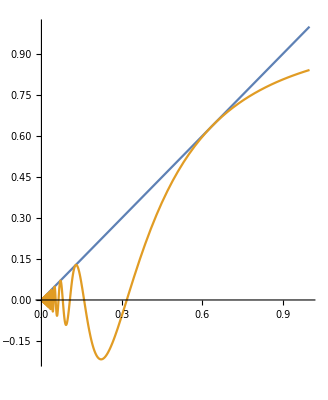

```mathematica
f2[x0_] := x0 * Sin[1/ x0]
Plot[{x, f2[x]}, {x, 0, 1}, AspectRatio->Full]
```

3) Narysuj wykresy funkcji pochodnych f’ z zadania 2.

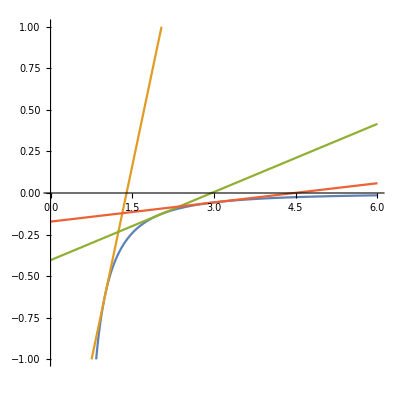

```mathematica
styczna1[x_, x0_] := f1'[x0] * (x - x0) + f1[x0];
Plot[{f1[x], styczna1[x, 1],styczna1[x, 2], styczna1[x,3]}, {x, 0, 6}, AspectRatio->1, PlotRange->1]
```

b. f2(x) = x sin(1/x) nie jest zdefiniowany w punkcie x = 0 ,  nie ma pochodny, ale mozemy narysowac styczna w punkcie x = 0.00001 ( blisko do 0 )

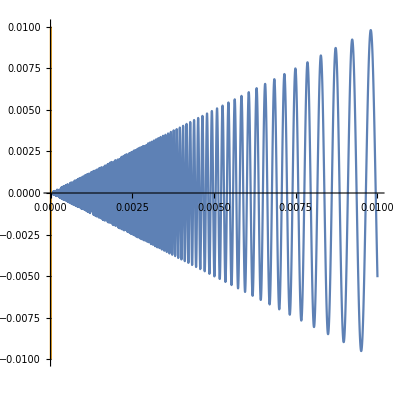

```mathematica
styczna2[x_, x0_] := f2'[x0] * (x - x0) + f2[x0]
Plot[{f2[x],styczna2[x,0.00001]},{x,0,0.01},AspectRatio->1,PlotRange->0.01]
```